```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
<< Combinatorica`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag Element in a_List∈{index___} is Protected.

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Global`

```mathematica
ga=RoachGraph[10]
ga = SetVertexWeights[ga, Table[1/V[ga],V[ga]]]
VertexWeights[ga]
(*ShowGraph[ga]*)
```

⁃Graph:<23,20,Undirected>⁃

⁃Graph:<23,20,Undirected>⁃

{1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20}

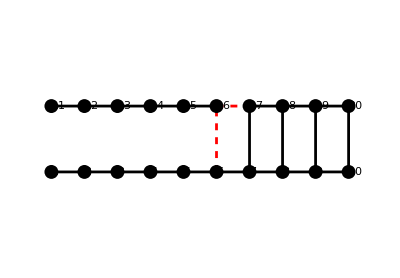

```mathematica
GraphPartition`ShowSpectralCut[ga]
FiedlerVector[ga]
(* what are the actual score in the sweep cut
*)GraphPartition`ShowIsoperimetricCut[SetVertexWeights[ga]]
GraphPartition`ShowMultipleFiedlerCut[ga]
(*
ShowGraph[GraphPartition`MultipleFiedlerCut[ga]]

*)
```

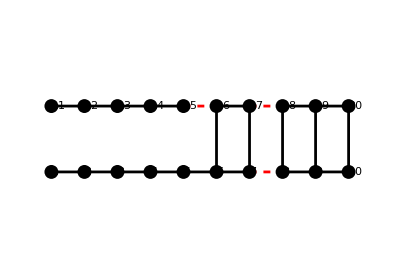

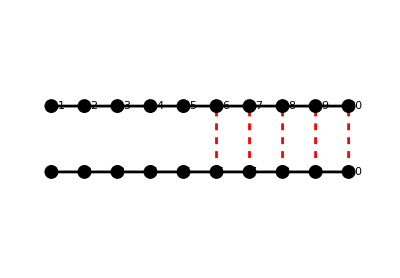

```mathematica
{0.40918635159651134,0.380020550398621,0.3237678148961186,0.2444377023337704,0.14768466888532764,0.040405033863103464,0.01105549469010167,0.003028936306558162,0.0008443553729352688,0.0002883016017182509,-0.40918635159650696,-0.38002055039861754,-0.3237678148961161,-0.24443770233376955,-0.14768466888532883,-0.040405033863106836,-0.01105549469010684,-0.003028936306564904,-0.0008443553729435061,-0.00028830160172692776}
```

```mathematica
ga=SetVertexWeights[ga,Table[1,1/V[ga]]]
EvaluatePartitionAlg[alg_,g_] := Switch[alg,
SpectralAlg,
Flatten[Timing[SpectralEdges[g, IncludeObj->True]],1],
IsoperimetricAlg,
Flatten[Timing[IsoperimetricEdges[g, IncludeObj->True]],1],
MultipleFiedlerAlg,
Flatten[Timing[MultipleFiedlerEdges[g, IncludeObj->True]],1](*
EvaluateMultipleFiedlerEdges[ga]*)
]
```

⁃Graph:<23,20,Undirected>⁃

⁃Graph:<23,20,Undirected>⁃

{1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20}

{0.015625,200/21,{{16,17},{6,16}}}

-Graphics-

{0.03125,8,{{5,6},{15,16}}}

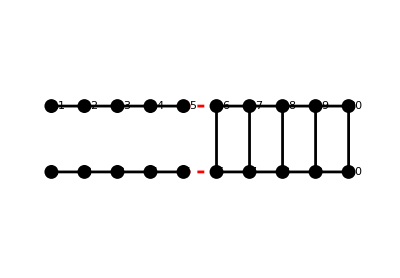

{0.015625,20,{{6,16},{7,17},{8,18},{9,19},{10,20}}}

-Graphics-

{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0}

{1/2,1/2}

```mathematica
ga=SetVertexWeights[ga,Table[1/V[ga],V[ga]]]
VertexWeights[ga]
{t, objFn, cutEdges}=EvaluatePartitionAlg[SpectralAlg,ga ]
ShowCuttedEdges[ga, cutEdges]
(*ShowCuttedEdges[ga,cutEdges]
v=FiedlerVector[ga]
c=CriterionCut[ga,v]
partitionWeights=PartitionWeights[VertexWeights[ga],v,c]
Total[Map[LookupWeight[ga,#]&,VectorCut[ga,v,c]]]
*){t, objFn, cutEdges}=EvaluatePartitionAlg[IsoperimetricAlg,ga ]
ShowCuttedEdges[ga, cutEdges]
{t, objFn, cutEdges}=EvaluatePartitionAlg[MultipleFiedlerAlg,ga ]

ShowCuttedEdges[ga, cutEdges]
v=MultipleFiedlerVector[ga]
partitionWeights=PartitionWeights[VertexWeights[ga],v,0.5]
```

```mathematica
Plot performances on RoachGraphs
```

```mathematica
graphs = Map[SetVertexWeights[RoachGraph[#],Table[1/(#*2),#*2]]&, Range[10,100,10]]
SpectralMetrics = Map[EvaluatePartitionAlg[SpectralAlg, #]&, graphs];
SpectralTimes = Transpose[SpectralMetrics][[1]]
SpectralObjs = Transpose[SpectralMetrics][[2]]
IsoperimetricMetrics = Map[EvaluatePartitionAlg[IsoperimetricAlg, #]&, graphs];
IsoperimetricTimes = Transpose[IsoperimetricMetrics][[1]]
IsoperimetricObjs = Transpose[IsoperimetricMetrics][[2]]
MultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg, #]&, graphs];
MultipleFiedlerTimes = Transpose[MultipleFiedlerMetrics][[1]]
MultipleFiedlerObjs = Transpose[MultipleFiedlerMetrics][[2]]
```

{⁃Graph:<23,20,Undirected>⁃,⁃Graph:<48,40,Undirected>⁃,⁃Graph:<73,60,Undirected>⁃,⁃Graph:<98,80,Undirected>⁃,⁃Graph:<123,100,Undirected>⁃,⁃Graph:<148,120,Undirected>⁃,⁃Graph:<173,140,Undirected>⁃,⁃Graph:<198,160,Undirected>⁃,⁃Graph:<223,180,Undirected>⁃,⁃Graph:<248,200,Undirected>⁃}

{0.,0.03125,0.0625,0.125,0.3125,0.453125,0.65625,0.84375,1.01563,1.23438}

{200/21,100/7,18000/779,11200/351,625/17,16000/351,58800/1081,1600/27,486000/7139,170000/2211}

{0.015625,0.046875,0.0625,0.125,0.1875,0.265625,0.375,0.484375,0.59375,0.734375}

{200/21,3200/399,8,6400/533,8,8,12,8,12,12}

{0.,0.03125,0.0625,0.078125,0.15625,0.25,0.34375,0.53125,0.640625,0.828125}

{20,40,60,80,100,120,140,160,180,200}

{Spectral,Isoperimetric,MultipleFiedler}

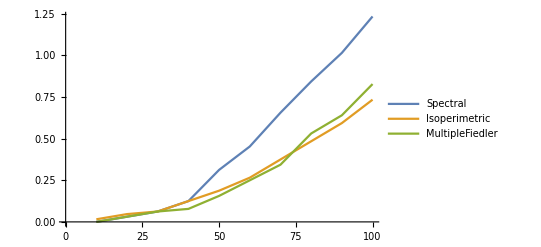

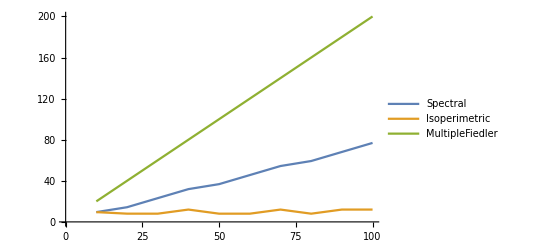

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes},PlotLegends->legends, DataRange->{10,100}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs}, PlotLegends->legends, DataRange->{10,100}]
```

```mathematica
graphs = Map[SetVertexWeights[RandomTree[#],Table[1/#,#]]&, Range[10,100,10]]
SpectralMetrics = Map[EvaluatePartitionAlg[SpectralAlg, #]&, graphs];
SpectralTimes = Transpose[SpectralMetrics][[1]]
SpectralObjs = Transpose[SpectralMetrics][[2]]
IsoperimetricMetrics = Map[EvaluatePartitionAlg[IsoperimetricAlg, #]&, graphs];
IsoperimetricTimes = Transpose[IsoperimetricMetrics][[1]]
IsoperimetricObjs = Transpose[IsoperimetricMetrics][[2]]
MultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg, #]&, graphs];
MultipleFiedlerTimes = Transpose[MultipleFiedlerMetrics][[1]]
MultipleFiedlerObjs = Transpose[MultipleFiedlerMetrics][[2]]
```

{⁃Graph:<9,10,Undirected>⁃,⁃Graph:<19,20,Undirected>⁃,⁃Graph:<29,30,Undirected>⁃,⁃Graph:<39,40,Undirected>⁃,⁃Graph:<49,50,Undirected>⁃,⁃Graph:<59,60,Undirected>⁃,⁃Graph:<69,70,Undirected>⁃,⁃Graph:<79,80,Undirected>⁃,⁃Graph:<89,90,Undirected>⁃,⁃Graph:<99,100,Undirected>⁃}

{0.015625,0.,0.015625,0.03125,0.03125,0.046875,0.046875,0.078125,0.09375,0.109375}

{4,4,225/56,25/6,2500/609,4,4900/1189,6400/1519,2025/506,10000/2499}

{0.,0.015625,0.03125,0.03125,0.046875,0.078125,0.078125,0.109375,0.140625,0.171875}

{4,4,225/56,25/6,2500/609,4,4900/1189,6400/1519,2025/506,10000/2499}

{0.,0.015625,0.015625,0.015625,0.03125,0.046875,0.078125,0.078125,0.125,0.15625}

{8,8,8,20,40,16,28,24,32,40}

{Spectral,Isoperimetric,MultipleFiedler}

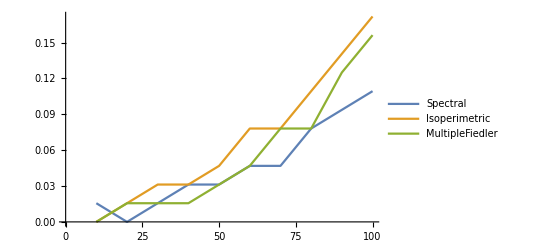

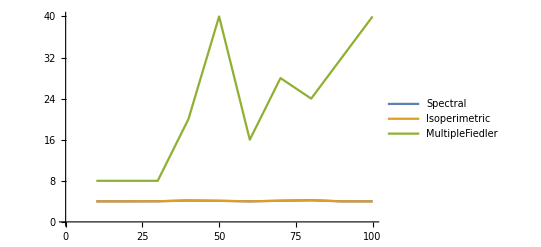

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes},PlotLegends->legends, DataRange->{10,100}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs}, PlotLegends->legends, DataRange->{10,100}]
```

```mathematica
SpectralMetrics = Table[EvaluatePartitionAlg[SpectralAlg, graph],{graph,graphs}]
```

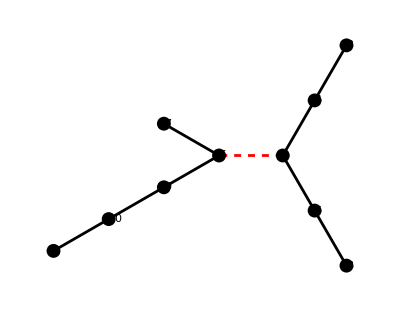

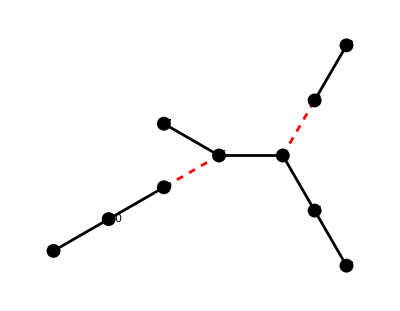

```mathematica
ShowSpectralCut[graphs[[1]]]
ShowMultipleFiedlerCut[graphs[[1]]]
```

# Small experiments 1. Develop evaluation matrix - Runtime - ObjectiveFunction - Parameters Spectral Partitioning - Isoperimetric Partitioning -> The Ground Vertex -> The number of iterations Multiple Fiedler Vector -> The # of eigenvectors -> Spectral Vertex Choice heuristic 2. Find dataset & benchmarks -> RandomTree, RoachGraphs -> DIMACS Graph Partitioning and Graph Clustering http://www.cc.gatech.edu/dimacs10/downloads.shtml -> Chris Walshaw’s graph partitioning archive http://chriswalshaw.co.uk/partition/ http://www.cc.gatech.edu/dimacs10/archive/data/walshaw/ -> Graph partitioning training examples http://eniac.cyi.ac.cy/display/UserDoc/Graph+Partitioning+Training+Examples#GraphPartitioningTrainingExamples-Example1

Why multiple Fiedler is performing worse.
VectorParition : how to decide eta
Metrics : time, CriterionFunction
Other data to test on

```mathematica
1)Generate normal graph data
```

- walk through every vertex and connect with 3 other random vertex
*- points on grid and connect with points within distance
(with locality)
- triangulation hhfhk

```mathematica
2) Debug spectral &  multiple fielder
```

```mathematica
currency in Canada US not let to use card or (insisting on 1 currency )
```